# Задача 4. Удельная поверхность углеродных нанообъектов

Получить выражение и рассчитать величину удельной поверхности массива из нанопластин однослойного графена, принимая длину элементарных векторов трансляции решетки графена – 0,246 нм, массу атома углерода – 12 а.е.м. = 19,92 10^24 г.

Получить выражение для величины удельной поверхности (наружной) массива из двухслойных УНТ, принимая расстояние между графеновыми слоями равным 0, 335 нм, длину элементарных векторов трансляции решетки графена – 0, 246 нм, массу атома углерода – 12 а.е.м. = 19, 92 10^24г. Получить численное значение величины удельной поверхности таких УНТ для случая, когда внешний диаметр всех УНТ равен 6 нм.

## Решение

### Массив из нанопластин однослойного графена

Схема пластин:

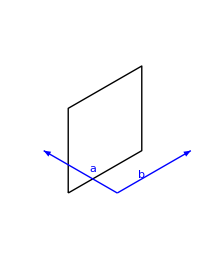

```mathematica
Graphics[{
Line[{{0,0},{1.5,Sin[60°]},{1.5,3Sin[60°]},{0,2Sin[60°]},{0,0}}],
Blue,
Arrow[{{1,0},{5Cos[60°],Sin[60°]}}],
Arrow[{{1,0},{-Cos[60°],Sin[60°]}}],
Text["a",{0.5,0.5}],
Text["b",{1.5,Sin[60°]-0.5}],
Transparent,
EdgeForm[Thick],
RegularPolygon[{0,0},1,6],
RegularPolygon[{1.5,Sin[60°]},1,6],
RegularPolygon[{0,2Sin[60°]},1,6],
RegularPolygon[{1.5,3Sin[60°]},1,6]

}]
```

Длина вектора трансляции:

```mathematica
b=Quantity[0.246,"Nanometers"];
```

Длины обоих векторов трансляции равны:

```mathematica
a=b;
```

Масса атома углерода:

```mathematica
mC=Quantity[12,"AtomicMassUnit"];
```

Площадь одного правильного треугольника с атомом углерода внутри:

```mathematica
S1=Area[Triangle[{{0,0},{g,0},{g/2,Sin[60°]*g}}]];
S1/.g->"a"//TraditionalForm
S1=S1/.g->a
```

(√3 Abs[a]^2)/4

0.0262042 nm^2

Тогда удельная площадь будет считаться по формуле (двойка за счет того, что поверхность берется с двух сторон):

S_ул=2 S/m_C

и численно будет равна:

```mathematica
UnitConvert[#,("Meters")^2/"Grams"]&@((2S1)/mC)//ScientificForm
```

2.63009×10^3 m^2/g

### УНТ

Схема трубок:

```mathematica
Graphics3D[{Gray,CapForm[None],
Tube[{{0,0,0},{5,0,0}},1],
Tube[{{0,0,0},{5,0,0}},0.5],
Black,
Arrow[{{0,0,0},{0,0.5,0}}],
Arrow[{{0,0,0},{0,0,1}}],
Arrowheads[{-0.03,0.03}],
Arrow[{{0,1.1,0},{5,1.1,0}}],
Arrow[{{0,0.5,0},{0,1,0}}],
Orange,
Text[Style["d",Large],{0,0.75,0.2}],
Text[Style["R_1",Large],{0,0.25,0.2}],
Text[Style["l",Large],{2.5,1.2,0}],
Text[Style["R_2",Large],{0,0.1,0.5}]
}]
```

-Graphics3D-

Площадь внешней трубки будет равна:

```mathematica
SExt=2π R2 l
```

2 l π R2

Площадь внутренней трубки:

```mathematica
SInt=2π R1 l
```

2 l π R1

Тогда масса всей трубки будет (здесь ρ - обратная удельная площадь на один треугольник из первой части задачи, однако составляющая только S_уд/2 поскольку мы рассматриваем только одну поверхность):

```mathematica
mAll=ρ*(SExt+SInt)
```

(2 l π R1+2 l π R2) ρ

Из нее можно получить длину трубки:

```mathematica
l=l/.Solve[m==mAll,l][[1,1]]
```

m/(2 π (R1+R2) ρ)

Выражение для удельной внешней поверхности будет иметь вид:

```mathematica
SExtUd=SExt/m
```

R2/((R1+R2) ρ)

Теперь нужно найти обратную удельную площадь одного треугольника. Это можно сделать исходя из масс.08ы атома и площади треугольника содержащего один атом:.08

```mathematica
ρ=mC/S1
```

457.942 u/nm^2

Расстояние между слоями трубки:

```mathematica
d=Quantity[0.335,"Nanometers"];
```

Внешний радиус трубок:

```mathematica
R2=Quantity[6,"Nanometers"]/2;
```

Радиус внутренней трубки:

```mathematica
R1=R2-d
```

2.665 nm

Теперь численно удельная площадь внешней поверхности будет равна:

```mathematica
UnitConvert[SExtUd,("Meters")^2/"Grams"]
```

696.405 m^2/g